# Prepare

```mathematica
imgsize=800;
SetDirectory@NotebookDirectory[];
```

```mathematica
Get["../../neupackage/mma/neutrino.wl"]
```

```mathematica
Get["../../neupackage/mma/neumat.wl"]
```

Parameters

```mathematica
endpoint=1000000;
deltamsquare13=2.6*10^(-15);(*MeV^2*)
energy10=10;(*Energy in units of MeV*)
energy20=20;(*Energy in units of MeV*)
?OmegaVacuum
omegaV=OmegaVacuum[energy10,deltamsquare13](*MeV*)(*deltamsquare13/(2 energy20)(*MeV*)*)(*For 10 MeV neutrinos*)
thetaV=ArcSin[√0.093]/2
```

Takes [energy_,deltam2_] as parameters and calculates ω_v. Should becareful about units.

1.3×10^-16

0.154948

```mathematica
energy20=20;(*Energy in units of MeV*)
```

```mathematica
fraction=1(*0.99*)
lambdaN=fraction*Cos[2thetaV]omegaV (*MeV*)
```

1

1.23808×10^-16

```mathematica
thetamVN=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaN/omegaV)^2)]/2,Pi];
```

```mathematica
omegaVKK=OmegaVacuum[energy20,deltamsquare13](*MeV*)(*deltamsquare13/(2 energy20)(*MeV*)*)
lambdaNKK=0.5*Cos[2thetaV]omegaVKK (*MeV*)
omegaMKK=OmegaMatter2[lambdaNKK,thetaV,omegaVKK](*MeV*)
thetamV=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaNKK/omegaVKK)^2)]/2,Pi]
```

6.5×10^-17

3.09519×10^-17

3.67552×10^-17

0.198931

```mathematica
secondfrac=90;
onekListKK={1};
twokListKK={1,1/secondfrac};
oneaListKK=(*{0.1};*){0.02(MeVInverse2km[2Pi/(omegaMKK onekListKK[[1]])]/1500)^(5/3)};
twoaListKK=(*{0.1,0.1};*){0.02(MeVInverse2km[2Pi/(omegaMKK twokListKK[[1]])]/1500)^(5/3),0.02(MeVInverse2km[2Pi/(omegaMKK twokListKK[[2]])]/1500)^(5/3)};
(*{oneaListKK[[1]],10^(-5)}*)
onephiListKK={0};
twophiListKK={0,0};

endpointNReconstruct=960000
```

960000

```mathematica
twoaListKK
```

{0.0000357347,0.0645894}

```mathematica
Part[qValueOrderdList[listNGenerator[1,10],onekListKK,oneaListKK,onephiListKK,thetamV],1;;10]
Grid@%
```

{{{1},0.},{{-1},288905.},{{2},8.76971×10^9},{{-2},2.63091×10^10},{{3},2.12963×10^15},{{-3},4.25927×10^15},{{4},5.81805×10^20},{{-4},9.69676×10^20},{{5},1.88381×10^26},{{-5},2.82571×10^26}}

{1} | 0.
{-1} | 288905.
{2} | 8.76971×10^9
{-2} | 2.63091×10^10
{3} | 2.12963×10^15
{-3} | 4.25927×10^15
{4} | 5.81805×10^20
{-4} | 9.69676×10^20
{5} | 1.88381×10^26
{-5} | 2.82571×10^26

```mathematica
destructionQOrder=Part[qValueOrderdList[listNGenerator[2,10],twokListKK,twoaListKK,twophiListKK,thetamV],1;;10]
Grid@%
```

{{{1,0},0.},{{0,4},128.051},{{0,5},132.437},{{0,-4},139.963},{{0,-5},148.017},{{0,6},195.456},{{0,-6},223.378},{{0,3},237.155},{{0,-3},253.511},{{0,7},370.226}}

{1,0} | 0.
{0,4} | 128.051
{0,5} | 132.437
{0,-4} | 139.963
{0,-5} | 148.017
{0,6} | 195.456
{0,-6} | 223.378
{0,3} | 237.155
{0,-3} | 253.511
{0,7} | 370.226

```mathematica
Table[
{First@destructionQOrder[[n]],widthNList[First@destructionQOrder[[n]],twokListKK,twoaListKK,twophiListKK,thetamV]},{n,1,Length@destructionQOrder}]
Grid@%
```

{{{1,0},3.83423×10^-7},{{0,4},0.00746228},{{0,5},0.0071313},{{0,-4},0.00746228},{{0,-5},0.0071313},{{0,6},0.00477517},{{0,-6},0.00477517},{{0,3},0.00407609},{{0,-3},0.00407609},{{0,7},0.00249097}}

{1,0} | 3.83423×10^-7
{0,4} | 0.00746228
{0,5} | 0.0071313
{0,-4} | 0.00746228
{0,-5} | 0.0071313
{0,6} | 0.00477517
{0,-6} | 0.00477517
{0,3} | 0.00407609
{0,-3} | 0.00407609
{0,7} | 0.00249097

```mathematica
Table[
{First@destructionQOrder[[n]],MeVInverse2km[2Pi/(omegaMKK*widthNList[First@destructionQOrder[[n]],twokListKK,twoaListKK,twophiListKK,thetamV])]},{n,1,Length@destructionQOrder}]
Grid@%
```

{{{1,0},8.78313×10^7},{{0,4},4512.9},{{0,5},4722.36},{{0,-4},4512.9},{{0,-5},4722.36},{{0,6},7052.43},{{0,-6},7052.43},{{0,3},8261.97},{{0,-3},8261.97},{{0,7},13519.5}}

{1,0} | 8.78313×10^7
{0,4} | 4512.9
{0,5} | 4722.36
{0,-4} | 4512.9
{0,-5} | 4722.36
{0,6} | 7052.43
{0,-6} | 7052.43
{0,3} | 8261.97
{0,-3} | 8261.97
{0,7} | 13519.5

```mathematica
Table[
{First@destructionQOrder[[n]],bNList[First@destructionQOrder[[n]],twokListKK,twoaListKK,twophiListKK,thetamV]},{n,1,Length@destructionQOrder}];
Grid@%
```

{1,0} | 0.-3.83423×10^-7 ⅈ
{0,4} | -0.00746228
{0,5} | 0.+0.0071313 ⅈ
{0,-4} | 0.00746228
{0,-5} | 0.-0.0071313 ⅈ
{0,6} | 0.00477517
{0,-6} | -0.00477517
{0,3} | 0.-0.00407609 ⅈ
{0,-3} | 0.+0.00407609 ⅈ
{0,7} | 0.-0.00249097 ⅈ

```mathematica
widthNList[{1,0},{1,1/7000},twoaListKK3,twophiListKK,thetamV]
twoaListKK
```

MapThread::mptd: Object twoaListKK3 at position {2, 3} in MapThread[BesselJ[#1, #3\ Cos[2\ 0.198931]/#2] &, {{1, 0}, {1, 1/7000}, twoaListKK3}] has only 0 of required 1 dimensions.

{{0.420276 Abs[BesselJ[#1,(#3 Cos[2 0.198931])/#2]&],0.},{0.420276 Abs[BesselJ[#1,(#3 Cos[2 0.198931])/#2]&],0.0000600395 Abs[BesselJ[#1,(#3 Cos[2 0.198931])/#2]&]},0.420276 Abs[twoaListKK3 (BesselJ[#1,(#3 Cos[2 0.198931])/#2]&)]}

{0.0000357347,0.0645894}

```mathematica
widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV]
widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV]*1000
twoaListKK[[1]]
MeVInverse2km[2Pi/(omegaMKK*%)]
```

6.92269×10^-6

0.00692269

0.0000357347

942404.

```mathematica
twoaListKK
```

{0.0000357347,0.0645894}

```mathematica
widthNList[{1,1},twokListKK,twoaListKK,twophiListKK,thetamV]
```

2.42186×10^-6

Second Freq As BG

```mathematica
pltNList[{{1}},onekListKK,oneaListKK,onephiListKK,thetamV,endpoint,"Mode n=1 with One Perturbation Only",Black,None,None]
```

```mathematica
pltNList[{{1}},onekListKK2,oneaListKK2,onephiListKK,thetamV2,endpoint,"Mode n=1 with Second Perturbation as Background",Black,None,None]
```

Parameter Set 3

Recalculate using some more mobile parameters, instead of the Komogorov spectrum

```mathematica
fractionk2=1/10;
fractionA2=20;
```

```mathematica
datafrac[fractionk2Input_,fractionA2Input_]:=Module[{fractionk2M,fractionA2M,solM},

fractionk2M=fractionk2Input;
fractionA2M=fractionA2Input;

twokListKK3={onekListKK[[1]],onekListKK[[1]]*fractionk2M};
twoaListKK3={oneaListKK[[1]],widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV]*fractionA2M};
lambdaNKK3=0.5*Cos[2thetaV]omegaVKK +twoaListKK3[[2]]*omegaMKK(*MeV*);
omegaMKK3=OmegaMatter2[lambdaNKK3,thetaV,omegaVKK](*MeV*);
thetamV3=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaNKK3/omegaVKK)^2)]/2,Pi];
onekListKK3=onekListKK[[1]]*omegaMKK/omegaMKK3;
oneaListKK3=(*{0.1};*)oneaListKK[[1]]*omegaMKK/omegaMKK3;


(*Part[qValueOrderdList[listNGenerator[1,10],onekListKK3,oneaListKK3,onephiListKK,thetamV3],1;;10];
Grid@%;
*)
(*widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV];
widthNList[{1},onekListKK2,oneaListKK2,onephiListKK,thetamV2];
*)


solM=Table[solNList[{{1}},{onekListKK3[[i]]},{oneaListKK3[[i]]},onephiListKK,thetamV3[[i]],endpoint],{i,1,Length@oneaListKK3}]

]
```

```mathematica
datafracStash=datafrac[{1/10,1/10,1/10},{10,20,30}]
datafracStash2=datafrac[{1/10,1/10,1/10},{100,1000,10000}]
datafracStash3=datafrac[{1/10^6},{10000}]
```

{{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}},{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}},{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}}

{{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}},{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}},{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}}

{{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}}

```mathematica
datafracStashFullTicks[i_]:=Table[{x,ScientificForm[MeVInverse2km[x/omegaMKK3[[1]]],2]},{x,0,endpoint}];
(*datafracStashTicks[i_]:=Take[datafracStashFullTicks[i],{1,Length@datafracStashFullTicks[i],Floor[(Length@datafracStashFullTicks[i])/5]}];*)
datafracStashTicks[i_]:=Table[{x,ScientificForm[MeVInverse2km[x/omegaMKK3[[1]]],2]},{x,0,endpoint,Floor[endpoint/5]}];
```

```mathematica
datafracStashTicks[1]
```

{{0,0.},{200000,1.1×10^6},{400000,2.3×10^6},{600000,3.4×10^6},{800000,4.5×10^6},{1000000,5.7×10^6}}

```mathematica
plotstylecolorList={Brown,Gray,Purple,Orange,Red,Blue}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[{Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.datafracStash[[1]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.datafracStash[[2]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.datafracStash[[3]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}]},Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks[1]}},
PlotLabel->"Resonance Destruction (k_2=k_1/10)",PlotLegends->Placed[{"A_2=10B_1","A_2=20B_1","A_2=30B_1"},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},PlotStyle->Take[plotstylecolorList,3]]
```

```mathematica
ListLogPlot[{Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.datafracStash[[1]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.datafracStash[[2]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.datafracStash[[3]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.datafracStash2[[1]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.datafracStash2[[2]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.datafracStash2[[3]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}]
},Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks[1]}},
PlotLabel->"Resonance Destruction (k_2=k_1/10)",PlotLegends->Placed[{"A_2=10B_1","A_2=20B_1","A_2=30B_1","A_2=100B_1","A_2=1000B_1","A_2=10000B_1"},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},PlotRange->{Automatic,{10^(-8),1}},PlotStyle->plotstylecolorList]
```

```mathematica
ListPlot[
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.datafracStash2[[2]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks[1]}},
PlotLabel->"Resonance Destruction (k_2=k_1/10)",PlotLegends->Placed[{"A_2=1000B_1"},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15}]
```

```mathematica
ListPlot[Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.datafracStash[[1]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks[1]}},
PlotLabel->"Resonance Destruction (k_2=k_1/10)",PlotLegends->Placed[{"A_2=1000000B_1"},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},PlotStyle->Take[plotstylecolorList,3]]
```

How about the numerical solution to the whole system?

```mathematica
twokListKK3Num={onekListKK[[1]],onekListKK[[1]]*{1/10,1/10,1/10,1/10,1/10,1/10}};
twoaListKK3Num={oneaListKK[[1]],widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV]*{10,20,30,100,1000,10000}};
```

```mathematica
{twoaListKK3Num[[1]],twoaListKK3Num[[2,6]]}
```

{0.0000357347,0.0692269}

```mathematica
solNumStash=Table[solNum[{twokListKK3Num[[1]],twokListKK3Num[[2,i]]},{twoaListKK3Num[[1]],twoaListKK3Num[[2,i]]},twophiListKK,thetamV,endpoint],{i,1,Length@twokListKK3Num[[2]]}]
```

$Aborted

```mathematica
ListLogPlot[{Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStash[[1]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStash[[2]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStash[[3]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStash[[4]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStash[[5]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStash[[6]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}]
},Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks[1]}},
PlotStyle->plotstylecolorList,PlotLabel->"Resonance Destruction (k_2=k_1/10)",PlotLegends->Placed[{"A_2=10B_1","A_2=20B_1","A_2=30B_1","A_2=100B_1","A_2=1000B_1","A_2=10000B_1"},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15}]
```

Check limits

```mathematica
twokListKK3NumLimit={onekListKK[[1]],onekListKK[[1]]*{1/100/Pi,1/100/Pi,1/100/Pi}};
twoaListKK3NumLimit={oneaListKK[[1]],widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV]*{1000,100,10000}};
```

```mathematica
solNumStashLimit=Table[solNum[{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,i]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,i]]},twophiListKK,thetamV,endpoint],{i,1,Length@twokListKK3NumLimit[[2]]}]
```

{{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}},{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}},{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}}

```mathematica
twokListKK3NumLimit10Mode=Table[solNList[{{1,0},{0,1},{0,-1}},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,i]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,i]]},twophiListKK,thetamV,endpoint],{i,1,Length@twokListKK3NumLimit[[2]]}]
```

{{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}},{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}},{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}}

```mathematica
gridlinesCode4[i_]:=Table[{n,Directive[plotstylecolorList[[i]],Dashed]},{n,0,endpoint,Pi/twokListKK3NumLimit[[2,i]]}]
```

TEMPTEMPTEP BEGIN

```mathematica
ListLogPlot[{Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[1]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[2]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[3]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.twokListKK3NumLimit10Mode[[1,1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.twokListKK3NumLimit10Mode[[2,1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.twokListKK3NumLimit10Mode[[3,1]]},{x,0,endpoint,Floor[endpoint/1000]}]
},Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks[1]}},
PlotStyle->{Red,Blue,Green,{Red,Dashing[{0.05,0.05}]},{Blue,Dashing[{0.03,0.03}]},{Green,Dashing[{0.03,0.03}]}},PlotLabel->"Resonance Destruction (k_2=k_1/(3Pi))",PlotLegends->Placed[{"A_2=1000B_1","A_2=100B_1","A_2=10000B_1","{1,0},{0,1},{0,-1} Mode with A_2=1000B_1","{1,0},{0,1},{0,-1} Mode with A_2=100B_1","{1,0},{0,1},{0,-1} Mode with A_2=10000B_1"},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},PlotRange->{Automatic,{10^(-9),10}}(*,GridLines->{gridlinesCode4[3], None},GridLinesStyle->Directive[Orange,Dashed]*)]
```

-Graphics-

```mathematica
ListPlot[{Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[1]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[2]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.twokListKK3NumLimit10Mode[[1,1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.twokListKK3NumLimit10Mode[[2,1]]},{x,0,endpoint,Floor[endpoint/1000]}]
},Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks[1]}},
PlotStyle->{Red,Blue,{Red,Dashing[{0.05,0.05}]},{Blue,Dashing[{0.03,0.03}]}},PlotLabel->"Resonance Destruction (k_2=k_1/10)",PlotLegends->Placed[{"A_2=1000B_1","A_2=1001B_1","{1,0} Mode with A_2=1000B_1","{1,0} Mode with A_2=1001B_1"},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},PlotRange->{Automatic,{10^(-9),10}}(*,GridLines->{gridlinesCode4[3], None},GridLinesStyle->Directive[Orange,Dashed]*)]
```

-Graphics-

```mathematica
twoaListKK3NumLimit[[2,2]]
twoaListKK3NumLimit[[2,1]]
```

0.00692961

0.00692269

```mathematica
Table[{twoaListKK3NumLimit[[1]]/twokListKK3NumLimit[[1]]Cos[2thetamV],twoaListKK3NumLimit[[2,i]]/twokListKK3NumLimit[[2,i]]Cos[2thetamV]},
{i,1,Length@twokListKK3NumLimit[[2]]}]

Table[{BesselJ[1,twoaListKK3NumLimit[[1]]/twokListKK3NumLimit[[1]]Cos[2thetamV]],BesselJ[0,twoaListKK3NumLimit[[2,i]]/twokListKK3NumLimit[[2,i]]Cos[2thetamV]]},
{i,1,Length@twokListKK3NumLimit[[2]]}]

Table[widthNList[{1,0},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,i]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,i]]},twophiList,thetamV],
{i,1,Length@twokListKK3NumLimit[[2]]}]
```

{{0.0000329435,0.0601486},{0.0000329435,0.00601486},{0.0000329435,0.601486}}

{{0.0000164718,0.999096},{0.0000164718,0.999991},{0.0000164718,0.911578}}

{6.91643×10^-6,6.92263×10^-6,6.31057×10^-6}

```mathematica
(*Test Theory and Prediction*)
probTheory[nlist_,klist_,alist_,thetamatter_,x_]:=widthNList[nlist,klist,alist,twophiList,thetamatter]^2/(widthNList[nlist,klist,alist,twophiListKK,thetamatter]^2+(nlist.klist-1)^2)Sin[x√(widthNList[nlist,klist,alist,twophiList,thetamatter]^2+(nlist.klist-1)^2)/2]^2;
solNumMode=Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.twokListKK3NumLimit10Mode[[1,1]]},{x,0,endpoint,Floor[endpoint/1000]}];
solTheoryMode=Table[Table[{x,probTheory[{1,0},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,i]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,i]]},thetamV,x]},{x,0,endpoint,Floor[endpoint/1000]}],{i,1,Length@twokListKK3NumLimit[[2]]}];

ListPlot[{solNumMode,solTheoryMode[[1]],solTheoryMode[[2]]},Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks[1]}},
PlotStyle->{Red,Blue,{Red,Dashing[{0.05,0.05}]},{Blue,Dashing[{0.03,0.03}]}},PlotLabel->"Resonance Destruction (k_2=k_1/10)",PlotLegends->Placed[{"A_2=1000B_1","A_2=1001B_1","{1,0} Mode with A_2=1000B_1","{1,0} Mode with A_2=1001B_1"},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},PlotRange->{Automatic,{10^(-9),10}}(*,GridLines->{gridlinesCode4[3], None},GridLinesStyle->Directive[Orange,Dashed]*)]
```

-Graphics-

### Calculate Widths, Q values, and more

```mathematica
BesselJ[0,10001Cos[2thetamV]]/BesselJ[0,10000Cos[2thetamV]]
```

-0.0573294

```mathematica
BesselJ[0,1001Cos[2thetamV]]/BesselJ[0,1000Cos[2thetamV]]
```

0.0367574

```mathematica
Part[qValueOrderdList[listNGenerator[2,20],{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,3]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,3]]},twophiListKK,thetamV],1;;10]
Grid@%
```

{{{1,0},0.},{{0,18},155.733},{{0,19},167.275},{{0,-18},174.664},{{0,17},180.519},{{0,-19},188.811},{{0,-17},201.173},{{0,20},209.025},{{0,-20},237.448},{{0,13},271.102}}

{1,0} | 0.
{0,18} | 155.733
{0,19} | 167.275
{0,-18} | 174.664
{0,17} | 180.519
{0,-19} | 188.811
{0,-17} | 201.173
{0,20} | 209.025
{0,-20} | 237.448
{0,13} | 271.102

```mathematica
twoaListKK3NumLimit[[2,3]]/twokListKK3NumLimit[[2,3]]Cos[2thetamV]
```

20.0495

```mathematica
10000widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV]
```

0.0692269

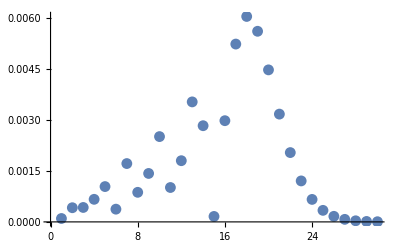

```mathematica
ListPlot[Table[widthNList[{0,n},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,3]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,3]]},twophiListKK,thetamV],{n,1,30}],GridLines->{None,{10000widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV]}}]
```

```mathematica
widthList10000={widthNList[{1,0},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,3]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,3]]},twophiListKK,thetamV],
widthNList[{0,1},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,3]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,3]]},twophiListKK,thetamV],
widthNList[{0,2},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,3]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,3]]},twophiListKK,thetamV]}
```

{1.13196×10^-6,0.000100129,0.000417517}

```mathematica
Part[qValueOrderdList[listNGenerator[2,10],{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,2]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,2]]},twophiListKK,thetamV],1;;10]
Grid@%
```

{{{1,0},0.},{{1,1},4595.2},{{1,-1},4624.55},{{0,1},7470.33},{{0,-1},7518.04},{{0,2},74156.3},{{0,-2},75106.5},{{1,2},182468.},{{1,-2},184806.},{{-1,0},291830.}}

{1,0} | 0.
{1,1} | 4595.2
{1,-1} | 4624.55
{0,1} | 7470.33
{0,-1} | 7518.04
{0,2} | 74156.3
{0,-2} | 75106.5
{1,2} | 182468.
{1,-2} | 184806.
{-1,0} | 291830.

```mathematica
widthList100={widthNList[{1,0},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,2]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,2]]},twophiListKK,thetamV],
widthNList[{0,1},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,2]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,2]]},twophiListKK,thetamV],
widthNList[{0,2},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,2]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,2]]},twophiListKK,thetamV]}
```

{6.85329×10^-6,0.000133437,0.0000133992}

```mathematica
Part[qValueOrderdList[listNGenerator[2,10],{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,1]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,1]]},twophiListKK,thetamV],1;;10]
Grid@%
```

{{{1,0},0.},{{1,1},795.19},{{1,-1},800.268},{{0,2},1049.25},{{0,-2},1062.7},{{0,1},1292.72},{{0,-1},1300.98},{{0,3},1902.27},{{0,-3},1938.95},{{1,2},2581.77}}

{1,0} | 0.
{1,1} | 795.19
{1,-1} | 800.268
{0,2} | 1049.25
{0,-2} | 1062.7
{0,1} | 1292.72
{0,-1} | 1300.98
{0,3} | 1902.27
{0,-3} | 1938.95
{1,2} | 2581.77

```mathematica
widthList1000={widthNList[{1,0},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,1]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,1]]},twophiListKK,thetamV],
widthNList[{0,1},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,1]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,1]]},twophiListKK,thetamV],
widthNList[{0,2},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,1]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,1]]},twophiListKK,thetamV]}
```

{1.53015×10^-6,0.000771098,0.000946993}

```mathematica
Grid@{widthList100,widthList1000,widthList10000}
```

6.85329×10^-6 | 0.000133437 | 0.0000133992
1.53015×10^-6 | 0.000771098 | 0.000946993
1.13196×10^-6 | 0.000100129 | 0.000417517

TEMPTEMPTEP END

```mathematica
ListLogPlot[{Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[1]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[2]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[3]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
(*Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[4]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],*)
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.twokListKK3NumLimit10Mode[[2,1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.twokListKK3NumLimit10Mode[[3,1]]},{x,0,endpoint,Floor[endpoint/1000]}](*,
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.twokListKK3NumLimit10Mode[[4,1]]},{x,0,endpoint,Floor[endpoint/1000]}]*)
},Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks[1]}},
PlotStyle->Join[Take[plotstylecolorList,3],{Directive[plotstylecolorList[[2]],Dashed],Directive[plotstylecolorList[[3]],Dashed],Directive[plotstylecolorList[[3]],Dashed]}],PlotLabel->"Resonance Destruction (A_2=10000B_1)",PlotLegends->Placed[{"k_2=k_1/10","k_2=k_1/1000","k_2=k_1/10000","k_2=k_1/20000","{1,0} Mode with k_2=k_1/1000","{1,0} Mode with k_2=k_1/10000","{1,0} Mode with k_2=k_1/20000"},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},PlotRange->{Automatic,{10^(-9),10}},GridLines->{gridlinesCode4[3], None},GridLinesStyle->Directive[Orange,Dashed]]
```

-Graphics-

```mathematica
ListLogPlot[{Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[1]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[2]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[3]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[4]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.twokListKK3NumLimit10Mode[[2,1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.twokListKK3NumLimit10Mode[[3,1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.twokListKK3NumLimit10Mode[[4,1]]},{x,0,endpoint,Floor[endpoint/1000]}]
},Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks[1]}},
PlotStyle->Join[Take[plotstylecolorList,4],{Directive[plotstylecolorList[[2]],Dashed],Directive[plotstylecolorList[[3]],Dashed],Directive[plotstylecolorList[[4]],Dashed]}],PlotLabel->"Resonance Destruction (A_2=10000B_1)",PlotLegends->Placed[{"k_2=k_1/10","k_2=k_1/1000","k_2=k_1/10000","k_2=k_1/20000","{1,0} Mode with k_2=k_1/1000","{1,0} Mode with k_2=k_1/10000","{1,0} Mode with k_2=k_1/20000"},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},PlotRange->{Automatic,{10^(-9),10}},GridLines->{gridlinesCode4[4], None},GridLinesStyle->Directive[Orange,Dashed]]
```

Part::partw: Part 4 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

$Aborted

Finally some figures about the actual matter profile

```mathematica
matterProfiles
```

{0.0000357347 Sin[0.0000357347 x],0.0000346135 Sin[x/10],0.0000692269 Sin[x/10],0.00010384 Sin[x/10],0.000346135 Sin[x/10],0.00346135 Sin[x/10],0.0346135 Sin[x/10]}

```mathematica
omegaMKK
```

3.67552×10^-17

```mathematica
matterProfilesTicks:=Table[{x,ScientificForm[MeVInverse2km[x/omegaMKK],2]},{x,0,Pi/twokListKK3Num[[1]],Pi/twokListKK3Num[[1]]/5}];

matterProfiles=Join[{twoaListKK3Num[[1]]*Sin[twokListKK3Num[[1]]x]},twoaListKK3Num[[2]]*Sin[twokListKK3Num[[2]]x]];
(*Plot[matterProfiles,{x,0,endpoint/10000},ImageSize->imgsize,PlotLegends->Placed[twoaListKK3Num[[2]],{Center,Above}],Frame->True,PlotRange->{{0,Pi/twokListKK3Num[[2,1]]},{10^(-6),0.1}},GridLines->{None, twoaListKK3Num[[2]]}]
*)
LogPlot[matterProfiles,{x,0,endpoint/10000},ImageSize->imgsize,PlotLegends->Placed[
Join[{twoaListKK3Num[[1]]},twoaListKK3Num[[2]]],{Center,Above}],Frame->True,PlotRange->{{0,Pi/twokListKK3Num[[1]]},{10^(-6),1}},PlotLabel->"Matter Profiles within Half Wavelength",PlotStyle->Join[{Black},plotstylecolorList],FrameLabel->{{"Matter Density (ω_m)",None},{"x̂","Distance (km)"}},FrameTicks->{{Automatic,Automatic},{Automatic,matterProfilesTicks}},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15}]
```

Some test of plotting

```mathematica
plotfrac[fractionk2Input_,fractionA2Input_,title_,legendsplotfrac_,color_]:=Module[{fractionk2M,fractionA2M},

fractionk2M=fractionk2Input;
fractionA2M=fractionA2Input;

twokListKK3={onekListKK[[1]],onekListKK[[1]]*fractionk2M};
twoaListKK3={oneaListKK[[1]],widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV]*fractionA2M};
lambdaNKK3=0.5*Cos[2thetaV]omegaVKK +twoaListKK3[[2]]*omegaMKK(*MeV*);
omegaMKK3=OmegaMatter2[lambdaNKK3,thetaV,omegaVKK](*MeV*);
thetamV3=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaNKK3/omegaVKK)^2)]/2,Pi];
onekListKK3=oneaListKK[[1]]*omegaMKK/omegaMKK3;
oneaListKK3=(*{0.1};*)oneaListKK[[1]]*omegaMKK/omegaMKK3;


(*Part[qValueOrderdList[listNGenerator[1,10],onekListKK3,oneaListKK3,onephiListKK,thetamV3],1;;10];
Grid@%;
*)
(*widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV];
widthNList[{1},onekListKK2,oneaListKK2,onephiListKK,thetamV2];
*)


Legended[Show[Table[pltNList[{{1}},{onekListKK3[[i]]},{oneaListKK3[[i]]},onephiListKK,thetamV3[[i]],endpoint,legendsplotfrac[[i]],color[[i]],None,None],{i,1,Length@oneaListKK3}],ImagePadding->{{Automatic, Automatic}, {Automatic, 20}},PlotLabel->title]
,Placed[LineLegend[color,legendsplotfrac],{Center,Above}]]

]
```

```mathematica
plotfrac[{1/10,1/10,1/10},{10,20,30},"Resonance Destruction (k2=k1/10)",{"A2=B1*10,A2=B1*20,A2=B1*30"},{Red,Blue,Orange}]
```

```mathematica
?pltNList
```

plot the result of solNList; Parameters taken are [listInput_,kNList_,aNList_,phiNList_,thetam_,endpoint_,legends_,color_,frameTicks_,frameLabel_,startpoint_:0]

```mathematica
(*pltNList[{{1}},onekListKK,oneaListKK,onephiListKK,thetamV,endpoint,"Mode n=1 with One Perturbation Only",Black,None,None];*)
solRes=solNList[{{1}},onekListKK,oneaListKK,onephiListKK,thetamV,endpoint];
```

```mathematica
solResList=Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solRes[[1]]},{x,0,endpoint,Floor[endpoint/1000]}];
```

```mathematica
solResList
```

Analytical

```mathematica
gRatio[n_]:=(n onekListKK[[1]]-1)^2/(n onekListKK[[1]]-omegaMKK2/omegaMKK)^2
gNew[n_]:=(n onekListKK[[1]]-omegaMKK2/omegaMKK)
```

```mathematica
tan2thetamRatio=(Tan[2thetamV])^2/(Tan[2thetamV2])^2
```

0.999985

```mathematica
besseljRatio[n_]:=BesselJ[n,oneaListKK[[1]]/onekListKK[[1]]Cos[2thetamV]]^2/BesselJ[n,oneaListKK2[[1]]/onekListKK2[[1]]Cos[2thetamV2]]^2
```

```mathematica
gNew[1]
gRatio[1]
besseljRatio[1]
```

8.42108×10^-6

0.

1.00002

Temp

```mathematica
Plot[{Sin[x],Sin[0.03x+Pi/10]},{x,0,Pi},Frame->True,ImageSize->imgsize,PlotLabel->Style["The Two Matter Perturbations",Black,FontSize->15],FrameTicks->None,PlotLegends->Placed[{"First Perturbation","Second Perturbation"},{Center, Above}]]
```

-Graphics-

```mathematica
N@twokListKK[[2]]
```

0.0111111

```mathematica
lambdaNKK/omegaVKK
```

0.476183

```mathematica
twoaListKK
```

{0.0000357347,1/100000}